## Setting

```mathematica
ClearAll[Evaluate[$Context<>"*"]]
Needs["ErrorBarPlots`"];

plotparameters=Evaluate[{Frame->True,BaseStyle->{FontSize->16,FontFamily->"Arial",FontColor->Black},LabelStyle->{FontSize->22,FontFamily->"Arial",FontColor->Black}},Axes -> {False, False}, Method->{"OptimizePlotMarkers"->False},FrameStyle->Thickness[0.003]];

SetOptions[Plot,plotparameters];
SetOptions[ListLinePlot,plotparameters];
SetOptions[ListPlot,plotparameters];
SetOptions[ErrorListPlot,plotparameters];
SetOptions[ListContourPlot,plotparameters];
SetOptions[ListLogLogPlot,plotparameters];
SetOptions[ListLogPlot,plotparameters];
SetOptions[Style,SingleLetterItalics->False];
verticalSize=250;
SetDirectory["~/Works/adaptive_potential/distribution/two_component/A_0125/"];
```

## Parameters and functions

```mathematica
L=8;
A=-Log[0.125]/L;
c = 3.5;
σ0=1;
d=0.4;
density=0.7;
densitySol=density;
dis=0.01;
τ=0.5;
β=1;
σ1=0.5;
σ2=1.5;
τ1=0.25;
τ2=0.25;
dis=0.01;
tol = 0.001;
den = 0;
ρ10=1;
ρ20=0.5654856738275738;
p2[σ_]:=Exp[-(σ-σ0)^2/τ^2]
ϕ[z_]:=A*z
B21[σ_,c_]:=c*σ^3
```

## two-component system

### initial condition of ideal gas (species 1)

```mathematica
q1=(density/L);
ρ1in=q1;
ρ1z=ConstantArray[0,{801,2}];
```

### perturb species 2 by species 1, vice versa

```mathematica
ρ2[z_,σ_]:=Exp[-2*ρ1in*B21[σ,c]-(σ-σ0)^2/τ^2]
ρ2data=Table[ρ2[z,σ],{z,0,L,dis},{σ,-4,5,dis}];
ρ2z=Table[{(z-1)*dis,Total[ρ2data[[z,All]]]*dis},{z,1,801,1}];
q = density/(Total[ρ2z[[All,2]]]*dis);
ρ2data[[All,All]]=ρ2data[[All,All]]*q;
ρ2z[[All,2]]=ρ2z[[All,2]]*q;
```

```mathematica
Do[
temp=0;
Do[
temp=temp+ρ2data[[z,Round[σ+4*100]+1]]*B21[σ,c]
,{σ,-4,5,dis}];
ρ1z[[z,All]]={(z-1)*dis,Exp[-2*temp*dis]};
,{z,1,801,1}]
q=densitySol/(Total[ρ1z[[All,2]]]*dis)
ρ1z[[All,2]]=ρ1z[[All,2]]*q;
```

4.44897

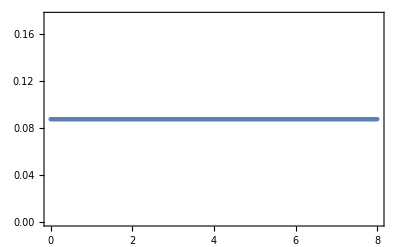

```mathematica
ListPlot[ρ1z]
```

### iterative perturbation

```mathematica
For[i=0,i<10,i++,
ρ2data=Table[Exp[-2*ρ1z[[Round[z*100+1],2]]*B21[σ,c]-(σ-σ0)^2/τ^2],{z,0,L,dis},{σ,-4,5,dis}];
q = density/(Total[Total[ρ2data[[All,All]]]]*dis*dis);
ρ2data[[All,All]]=ρ2data[[All,All]]*q;
ρ2z=Table[{(z-1)*dis,Total[ρ2data[[z,All]]]*dis},{z,1,801,1}];
Do[
temp=0;
Do[
temp=temp+ρ2data[[z,Round[(σ+4)*100]+1]]*B21[σ,c]
,{σ,-4,5,dis}];
ρ1z[[z,All]]={(z-1)*dis,Exp[-2*temp*dis-β*A*(z-1)*dis]};
,{z,1,801,1}];
q=densitySol/(Total[ρ1z[[All,2]]]*dis);
ρ1z[[All,2]]=ρ1z[[All,2]]*q;
]
```

General::munfl: 0.7 9.66318545341428×10^-4492 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.7 9.66318545276392×10^-4492 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

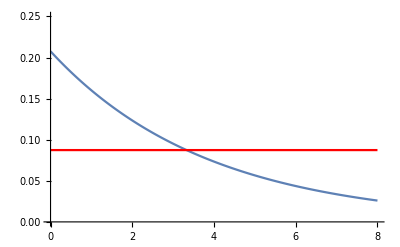

```mathematica
ρ2plot=ListLinePlot[ρ2z,PlotRange->{{0,L},{0,0.25}},PlotStyle->Red];
ρ1plot=ListLinePlot[ρ1z,PlotRange->{{0,L},{0,0.25}}];
Show[ρ1plot,ρ2plot]
```

```mathematica
Total[ρ2z]*dis
```

{32.04,0.7}

```mathematica
(*Export["rho_z_1_c"<>ToString[c]<>".txt",ρ1z];
Export["rho_z_2_c"<>ToString[c]<>".txt",ρ2z];*)
```

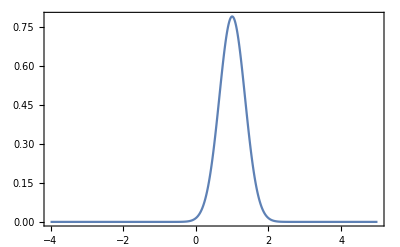

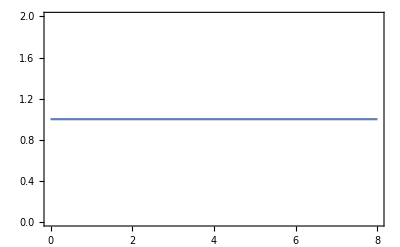

0.7

```mathematica
Nsig=Table[{σ,Total[ρ2data[[All,Round[(σ+4)*100+1]]]]*dis},{σ,-4,5,dis}];
sigztable=ConstantArray[0,{801,2}];
Do[
temp=0;
Do[
temp=temp+ρ2data[[Round[z*100+1],Round[(σ+4)*100+1]]]*σ
,{σ,-4,5,dis}];
sigztable[[Round[z*100+1],All]]={z,temp/ρ2z[[Round[z*100+1],2]]*dis};
,{z,0,L,dis}]
ListLinePlot[Nsig,PlotRange->{{-4,5},Full}]
ListLinePlot[sigztable]
Total[Total[ρ2data[[All,All]]]]*dis*dis
Export["N_sig_c"<>ToString[c]<>".txt",Nsig];
Export["sig_z_c"<>ToString[c]<>".txt",sigztable];
```

```mathematica
FindRoot[Exp[0]*0.25==Exp[-β*a*L],{a,0.1}]
```

{a→0.173287}